# On Proportional Braking in H Bridges

Robert Atkinson
10 August 2018

Most H bridge designs use one of two common switching modalities, which are commonly termed ‘lock anti-phase’ and ‘sign-magnitude’ respectively (Ref: http://www.modularcircuits.com/blog/articles/h-bridge-secrets). However, the STMicroelectronics VNH5050E H bridge, used in FTC motor controllers for nearly the past decade, employs neither of these modalities, instead using what can be called an ‘asynchronous sign-magnitude switching modality. In addition to it’s driving modes, this modality admits a mode wherein dynamic-braking is applied in proportional to the PWM duty cycle, which we term ‘proportional braking’.

## Section. Introduction

### Section.Subsection. Administrivia

Before we begin, we load in some previously computed logic.

```mathematica
Get[NotebookDirectory[] <> "Utilities.m"]
inputDirectory = FileNameJoin[{NotebookDirectory[],"MotorPhysicsGears.Output"}] <> $PathnameSeparator;
Get[inputDirectory <> "ParametersUnitsAndAssumptions.m"];
Get[inputDirectory <> "MotorModels.m"];
Get[inputDirectory <> "MotorTimeDomainFunctions.m"];
Get[inputDirectory <> "SteadyState.m"];
Get[inputDirectory <> "Misc.m"];
```

### Section.Subsection. H Bridge Architecture

In order to appreciate the design task explored in this document, it is important to have a comfortable, detailed working understanding of the operation of H bridges. From a simplified perspective, an H Bridge can abstractly be thought of as a circuit involving a motor, a voltage source, and four switches (Ref: https://en.wikipedia.org/wiki/H_bridge):

-Graphics-

In this document, we need to be able to discuss with some precision the state of these switches. As there are four switches, there are 16 possible states. We will number those states by assigning weights to each switch, and summing over the weights of the switches which are closed in any particular state. We assign weights as follows: S1 → 8,  S2 → 4,  S3 → 2,  and S4 → 1. With that nomenclature in hand, the motor’s response in each of the 16 states is as follows:

Note that in a design where an H bridge is driven by pulse width modulation, we can talk with precision about the operation of the bridge by naming the state used in the “on” part of the PWM cycle, the state used in the “off” part of the cycle, and the duty-cycle percentage of the “on” state as a fraction of the PWM framing period (which is contextually herein taken as fixed). Thus, for example, we might talk about an H bridge using a 6/2 mode being driven at a 75% duty cycle, or a bridge in 5/0 mode with a 30% duty cycle, etc.

States 9 and 6 are the driving states. In state 9, the motor turns one direction, which we have arbitrarily labeled as CW (or, more precisely, it attempts to increase its angular velocity in the CW direction). In state 6, the motor turns CCW. In state 0 it coasts, while in states 5 and 10 rheostatic dynamic braking is employed (Ref: https://en.wikipedia.org/wiki/Dynamic_braking), either through the ground rail or the power rail. Seven of the states are short circuits, and should be avoided.

States 8, 4, 2, and 1 deserve special mention. Their behavior is dependent not only on the state of the switches, but also on the sign of the instantaneous angular velocity.  This is due to consequences of the fact that a more complete picture of an H bridge must include the so-called ‘catch diodes’ whose presence is necessary to avoid inductive voltage spikes during switching transitions (Ref: http://modularcircuits.tantosonline.com/blog/articles/h-bridge-secrets/h-bridges-the-basics/).

-Graphics-

Let us consider state 8, where S1 (aka Q1) is closed, and the remaining switches are open. If we are driving CW, and, say, switching between state 9 and state 8 over a PWM frame (which we will denote as the 9/8 mode), then as switch S4 is opened, the inductive motor current briefly discharges across D1 (in FTC motors, ‘briefly’ is about 1ms). Because the shaft is turning CW, the polarity of the motor’s back EMF is such that it cannot drive current through that same route. All is well: we drive forward.

However, consider the case where we had been driving in the CCW direction, using, say, the 6/2 mode, so that the motor shaft is currently rotating CCW. Then, were we to switch to 9/8 mode, we find that the polarity of the motor’s back EMF is the other way around; it can now also drive current through the diode, and we find ourselves in a dynamic braking situation.

States 4, 2, and 1 have analogous behavior.

### Section.Subsection. Forward Driving vs Proportional Braking vs Reverse Driving

The STMicroelectronics VNH5050E H bridges used in FTC use 9/8 and 6/2 driving modes. Thus, the behaviors of states 8 & 2 mentioned above are pertinent.

Suppose we are driving CW, cruising along, forward driving using mode 9/8 (the 6/2 case is analogous), having developed some non-zero velocity in the shaft. Then, suppose further that our PID loop discerns that we’re going a little too fast. At first, it will ask us to take our foot off the gas a little, which we do by reducing the 9/8 duty cycle. But if after that we’re still going too fast, the PID loop will ask us to take stronger measures. What the current (August 2018) firmware does in response to that request is to start driving in the other direction (i.e. CCW, using mode 6/2). This we’ll call reverse driving (reverse in the sense that it’s opposite to the direction of the shaft rotation). Reverse driving brings in to play the ‘brake to VCC’ behavior of state 2.

The problem is that it’s impossible to decelerate gently drive using reverse driving. This is because even 6/2 reverse driving with only the minimum possible 0% duty cycle is effectively (except for a diode voltage drop) a fully dynamic braking situation; as we increase the duty cycle percentage, this braking is only augmented by additional motor torque actively driving backwards. The transition from 0% forward driving to 0% reverse driving is thus a very abrupt one.

With asynchronous sign-magnitude H bridges such as the VNH5050E there is a third mode we can avail ourselves of to help ease this transition: mode 5/0, which we call proportional braking. In state 5, S2 and S4 are closed, causing dynamic braking; in state 0, all switches are open. A 0% duty cycle proportional braking thus is a (zero-torque) open circuit where we coast, just we do in 0% 9/8 forward driving. At the other extreme, 100% proportional braking is full dynamic braking, just as 0% reverse driving is (again, ignoring the diode drop for the moment). In between, the balance of braking vs coasting is controlled by the PWM duty cycle. Thus, proportional braking provides a transitional regime between forward driving and reverse driving that we can exploit to respond smoothly to the PID loop’s request for increasing amounts of deceleration.

The design challenge is to select the points in the control signal coming from the PID loop where we transition from one regime to the other. There are four points of relevance, which are as follows.

R, the point of 100% reverse driving. It is is clear that this occurs at the negative extreme of the PID control signal range.

F, the point of 100% forward driving. This occurs at the positive extreme of the PID control signal range.

Z, the point of 0% proportional braking and 0% forward driving.

T, the point of 0% reverse driving and 100% proportional braking (we again ignore the diode for now).

In what follows, the location of either Z or T in the PID control range will be determined a priori based on external considerations, and the location of the remaining point then determined from the other three using arguments of linearity. We will examine three different schemes.

Some illustrations may help clarify. In the first Scheme A, Z is chosen to have an x value of zero and a positive velocity dependent Y value; T is on the negative control axis with a zero y value. Use of forward driving is illustrated in green, proportional braking in blue, and reverse driving in red.

```mathematica
Clear[plotScheme, line, points, pointNames]; 
line[{x1_, y1_}, {x2_, y2_}] := Function[{x}, y1 + (y2 - y1) / (x2 - x1) * (x - x1)]
points = { R -> {-controlMax, -yMax},  T -> { controlProp100, yProp100 }, Z -> {controlProp0, yProp0}, F-> {controlMax, yMax}};
pointNames = { R, T, Z, F};
schemeAExample = {controlProp100 -> - 2controlMax /3, yProp100 -> 0, controlProp0 -> 0, yProp0 -> 3 yMax / 4};
plotScheme[scheme_, title_, yAxis_] := Module[{scale = {controlMax -> 32767, yMax -> 100}, pointsN, listPlot, range, reverse, braking, forward},
pointsN = points //. scheme /. scale;
range[x_, p1_, p2_] := {x, (p1 /. pointsN)[[1]], (p2 /. pointsN)[[1]]};
listPlot = ListPlot[{ R -> "R", T -> "T", Z -> "Z", F-> "F"} /. pointsN, PlotRange-> {-yMax * 1.1, yMax * 1.1} /. scale, PlotStyle->Black, AxesLabel->{"control", yAxis}, PlotLabel->title];
reverse = Plot[Evaluate[line[R, T] /. pointsN][x], Evaluate[range[x, R, T]], PlotStyle->Red];
braking = Plot[Evaluate[line[T, Z] /. pointsN][x], Evaluate[range[x, T, Z]], PlotStyle->Blue];
forward = Plot[Evaluate[line[Z, F] /. pointsN][x], Evaluate[range[x, Z, F]], PlotStyle->Darker[Green]];
Show[listPlot, reverse, braking, forward]
]
plotScheme[schemeAExample, "Scheme A Example", "y"]
```

-Graphics-

In a second Scheme B, T is chosen to be at the origin, and Z has a positive X value and a velocity dependent positive Y value.

```mathematica
schemeBExample = {controlProp100 -> 0, yProp100 -> 0, controlProp0 -> 2controlMax /3, yProp0 -> 5 yMax / 6};
plotScheme[schemeBExample, "Scheme B Example", "y"]
```

-Graphics-

In a third Scheme C, Z is chosen to reside at the origin; T has a negative X value and a velocity dependent negative Y value

```mathematica
schemeCExample = {controlProp100 -> - 2controlMax /3, yProp100 -> - 1 yMax / 3, controlProp0 -> 0, yProp0 -> 0};
plotScheme[schemeCExample, "Scheme C Example", "y"]
```

-Graphics-

What’s important to take away from the above illustrations is not the actual coordinate values of the points, but rather their relative positioning along the control axis: whether they are in the negative control range, at zero, or in the positive control range. In particular, it is desirable that in real examples some points be colinear which are not illustrated so above.

Careful readers will also have noted that we have said nothing about what the Y axis represents. This is by design, as the interpretation of this axis will vary amongst the schemes. We will discuss this at some length below.

### Section.Subsection. On “Instantaneous Effective Applied Voltage” and “Instantanous Current”

## Section. Locating the Transition Point

### Section.Subsection. General

In the steady state (no acceleration), the back EMF is proportional to the steady state velocity Ω (in radians per second).

```mathematica
backEmfEqns = {ssEmf == Ke Ω}
```

{ssEmf==Ke Ω}

### Section.Subsection. Proportional Braking

We need to know the beginning and endpoints of the proportional braking curve, but here need not assume it is linear.

0% proportional braking is 100% H-bridge state 0. In that state, there is zero torque, as we have an open circuit. In order to determine the transition between proportional braking and reverse driving, rather than dealing with open circuits we will determine for each situation of relevance an equivalent instantaneous DC applied voltage for an H-bridge-less variant of the motor. For the zero-torque situation, we need to examine our voltage differential equation.

```mathematica
diffEqns[[3]]
```

R i[t]+vg[t]+L i'[t]==vapp[t]

If we’re in steady state at velocity Ω, and we instantaneously drop the voltage, to what level should we drop it so that the torque (and thus the current) as averaged over our PID loop execution interval (50ms) is zero? We haven’t yet completed that analysis, so for now we’ll use an approximation. If there is zero torque, there is zero current. Which means that drop across the resistor is zero. After a couple of time constants, the drop across the inductor will also be zero, and we’re left with:

```mathematica
diffEqns[[3]] /. {i[t] -> 0, i'[t] -> 0}
```

vg[t]==vapp[t]

That is, the voltage we should drop our applied voltage vappt[t] to is (approximately) the current back EMF. This is only approximate, as it doesn’t account for the exponential ramp down of the current, nor does it consider the deceleration of the motor (and consequent drop in the back EMF) that will happen over the PID loop interval, but it’s the best we have on hand for now.

We recall that this is happening at 0% proportional braking, which we wish to be coincident to the origin.

```mathematica
prop0Eqns = { controlProp0 == 0, voltProp0 == ssEmf }
```

{controlProp0==0,voltProp0==ssEmf}

At 100% proportional braking, we have shorted across the motor terminals; the instantaneous applied voltage is zero.

```mathematica
prop100Eqns = {voltProp100 == 0}
```

{voltProp100==0}

We define a linear curve for proportional braking, though in the below we only use it for plotting, not in the determination of the transition point.

```mathematica
voltProp[control_]  := voltProp0 + (voltProp100 - voltProp0) / (controlProp100 - controlProp0) * (control - controlProp0)
voltProp[controlProp100]
voltProp[controlProp0]
```

voltProp100

voltProp0

### Section.Subsection. Reverse Driving

0% reverse driving is almost the same as 100% proportional braking except that there’s a diode eating some of the voltage alongside the resistor and the inductor. Thus, going back to our differential equation above, the instantaneous equivalent applied voltage needs to be adjusted slightly positive to balance.

```mathematica
reverse0Eqns = { voltReverse0 == -(0 - diodeDrop) }
```

{voltReverse0==diodeDrop}

100% reverse driving applies the full negative battery voltage:

```mathematica
reverse100Eqns = { controlReverse100 == -controlMax, voltReverse100 == -batteryVoltage }
```

{controlReverse100==-controlMax,voltReverse100==-batteryVoltage}

### Section.Subsection. Continuity

We will assume linearity of reverse driving in order to set up our continuity of voltage (we only use that fact in the initial duty cycle range of reverse driving).

```mathematica
voltReverse[control_]  := voltReverse0 + (voltReverse100 - voltReverse0) / (controlReverse100 - controlReverse0) * (control - controlReverse0)
voltReverse[controlReverse100]
voltReverse[controlReverse0]
```

voltReverse100

voltReverse0

Because of the diode voltage drop, when we stitch proportional braking beside reverse driving so as to have a continuous overall voltage curve, there is necessarily a small overlap in the two curves: as we proceed from small to large control signal magnitude (remember that proportional braking and reverse driving are placed in the negative control signal range), the reverse driving curve begins before the proportional braking curve ends. That is, Abs[controlReverse0] <= Abs[controlProp100].

Here, we choose to use braking in the overlap. Thus, here our transition point is controlProp100.

```mathematica
controlTransition = controlProp100;
controlOther = controlReverse0;
```

Our continuity requirement is that at the transition, the two curves must coincide.

```mathematica
ctyEqns = { voltProp[controlTransition] == voltReverse[controlTransition] }
```

{voltProp100==voltReverse0+((controlProp100-controlReverse0) (-voltReverse0+voltReverse100))/(-controlReverse0+controlReverse100)}

### Section.Subsection. Linearity

All other things being equal, what we want is that the overall voltage vs control signal in the negative control range be as linear as possible. The shapes of the two curves, and the voltages at their endpoints is fixed; all we have to control is the transition threshold. We assume that the duty cycle response curves of both modes is linear. (While they’re not entirely so, they’re close, and we need to start somewhere. If we actually knew the curves we’d do a least squares fit.) Then, the overall concatenation can best be fit as  linear by matching the slopes of the proportional braking as a whole and the reverse driving as a whole.

```mathematica
slopeEqns = { 
slope == (voltProp100 - voltProp0) / (controlProp100 - controlProp0),
slope == (voltReverse100 - voltReverse0) / (controlReverse100 - controlReverse0)
}
```

{slope==(-voltProp0+voltProp100)/(-controlProp0+controlProp100),slope==(-voltReverse0+voltReverse100)/(-controlReverse0+controlReverse100)}

### Section.Subsection. Summary

We put all our equations together.

```mathematica
(eqns = Join[backEmfEqns, prop0Eqns, prop100Eqns, reverse0Eqns, reverse100Eqns, ctyEqns, slopeEqns]) // prettyPrint
```

ssEmf==Ke Ω
controlProp0==0
voltProp0==ssEmf
voltProp100==0
voltReverse0==diodeDrop
controlReverse100==-controlMax
voltReverse100==-batteryVoltage
voltProp100==voltReverse0+((controlProp100-controlReverse0) (voltReverse100-voltReverse0))/(controlReverse100-controlReverse0)
slope==(voltProp100-voltProp0)/(controlProp100-controlProp0)
slope==(voltReverse100-voltReverse0)/(controlReverse100-controlReverse0)

### Section.Subsection. Solving

We solve these equations.

```mathematica
solveFor = {controlTransition, controlOther, slope, voltProp0, voltProp100, voltReverse0,voltReverse100, controlProp0, controlReverse100, ssEmf};
soln = uniqueSolve[eqns, solveFor];
soln // prettyPrint
```

controlProp100→-(controlMax Ke Ω)/(batteryVoltage+Ke Ω)
controlReverse0→(controlMax diodeDrop-controlMax Ke Ω)/(batteryVoltage+Ke Ω)
slope→(batteryVoltage+Ke Ω)/controlMax
voltProp0→Ke Ω
voltProp100→0
voltReverse0→diodeDrop
voltReverse100→-batteryVoltage
controlProp0→0
controlReverse100→-controlMax
ssEmf→Ke Ω

### Section.Subsection. Results

#### Section.Subsection.Subsubsection. In Radians / Second & Battery Volts

The control transition point (and it’s dancing partner) we seek is the following:

```mathematica
result = {"controlTransition" -> controlTransition /. soln, "controlOther" -> controlOther /. soln} // Simplify
```

{controlTransition→-(controlMax Ke Ω)/(batteryVoltage+Ke Ω),controlOther→(controlMax (diodeDrop-Ke Ω))/(batteryVoltage+Ke Ω)}

#### Section.Subsection.Subsubsection. In Encoder Counts / Second & Battery mV

To implement the logic, we need the the result with a different measure of velocity and battery voltage.

```mathematica
tpsToRadiansPerSec[cps_] := Quantity[cps, IndependentUnit["counts"]/ "Seconds"] / Quantity[countsPerRev, IndependentUnit["counts"]/ "Revolutions"] * Quantity[2 Pi, "Radians" / "Revolutions"]
tpsToRadiansPerSec[cps]
```

(2 cps π)/countsPerRev rad/s

```mathematica
resultUnits = {
controlMax -> Quantity[controlMax, IndependentUnit["pids"]], 
batteryVoltage -> Quantity[mvBatteryVoltage, "Volts"] / 1000,
Ke -> Quantity[Ke, "Volt Seconds"] / Quantity[1, "Radians"],
diodeDrop-> Quantity[diodeDrop, "Volts"],
Ω -> tpsToRadiansPerSec[cps]
}
result/. resultUnits // Simplify
resultCps = result/. resultUnits // Simplify // clearUnits
```

{controlMax→controlMax pids,batteryVoltage→mvBatteryVoltage/1000 V,Ke→Ke s V/rad,diodeDrop→diodeDrop V,Ω→(2 cps π)/countsPerRev rad/s}

{controlTransition→-(2000 controlMax cps Ke π)/(countsPerRev mvBatteryVoltage+2000 cps Ke π) pids,controlOther→(1000 controlMax (countsPerRev diodeDrop-2 cps Ke π))/(countsPerRev mvBatteryVoltage+2000 cps Ke π) pids}

{controlTransition→-(2000 controlMax cps Ke π)/(countsPerRev mvBatteryVoltage+2000 cps Ke π),controlOther→(1000 controlMax (countsPerRev diodeDrop-2 cps Ke π))/(countsPerRev mvBatteryVoltage+2000 cps Ke π)}

To compute the value, we’ll first compute the transition, then compute the delta from the transition to the other control point

```mathematica
computedControlTransiton = "controlTransition" /. resultCps // Apart
```

-controlMax+(controlMax countsPerRev mvBatteryVoltage)/(countsPerRev mvBatteryVoltage+2000 cps Ke π)

```mathematica
ΔcomputedControlOther = ("controlOther" - "controlTransition") /. resultCps // Apart
```

(1000 controlMax countsPerRev diodeDrop)/(countsPerRev mvBatteryVoltage+2000 cps Ke π)

## Section. Verification

### Section.Subsection. Check

Let us verify that at the control transition point, the two curves coincide.

```mathematica
voltProp[controlTransition] - voltReverse[controlTransition]
% /. soln
% // FullSimplify
```

voltProp100-voltReverse0-((controlProp100-controlReverse0) (-voltReverse0+voltReverse100))/(-controlReverse0+controlReverse100)

-diodeDrop-((-batteryVoltage-diodeDrop) (-(controlMax Ke Ω)/(batteryVoltage+Ke Ω)-(controlMax diodeDrop-controlMax Ke Ω)/(batteryVoltage+Ke Ω)))/(-controlMax-(controlMax diodeDrop-controlMax Ke Ω)/(batteryVoltage+Ke Ω))

0

### Section.Subsection. In Real Life

We examine what this looks like for an actual motor. We choose a NeveRest 60. We ignore the gearing since we want the Ke relative to the pre-gearbox armature velocity, not the post-gearbox shaft velocity.

```mathematica
aMotor = motorParameters["AM 60 A", Geared -> False] // siUnits // clearUnits
constants = {diodeDrop -> 7/10, Ke -> (Ke /. aMotor), batteryVoltage -> 12, controlMax -> 32767}
```

<|R→33/10,L→347/500000,Ke→533/500,Kt→533/500,J→1041/100000000,B→33/1000,Ν→1,η→1,Jafter→0,Bafter→0,constτappafter→0|>

{diodeDrop→7/10,Ke→533/500,batteryVoltage→12,controlMax→32767}

There are three points of relevance to us.

```mathematica
points = {
Z -> {controlProp0, voltProp0},
T -> {controlProp100, voltProp100},
R -> {controlReverse100, voltReverse100}
}
```

{Z→{controlProp0,voltProp0},T→{controlProp100,voltProp100},R→{controlReverse100,voltReverse100}}

The maximum velocity of this motor is just over 10 radians / second.

```mathematica
ssVel /. ss /. aMotor /. constvapp -> batteryVoltage /. constants // N
```

10.2726

At that velocity, what part of the negative control range is devoted to proportional braking?

{Ω→10.27}

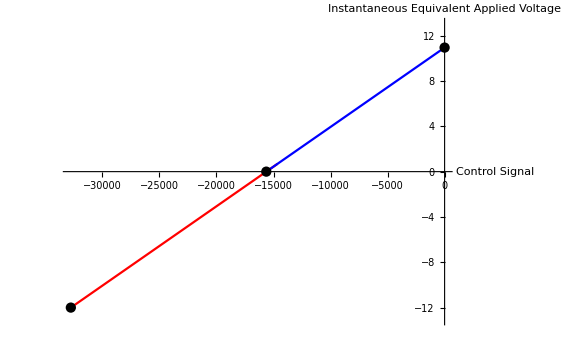

```mathematica
speed = {Ω -> 10.27}
all = Join[soln, constants, speed];
p1 = Plot[Evaluate[voltReverse[control] //. all], {control, controlReverse100, controlReverse0} //. all, PlotStyle->Red, AxesOrigin->{0,0}, PlotRange->Evaluate[{-batteryVoltage-1, batteryVoltage+1} //. all], 
AxesLabel->{HoldForm[Control Signal], HoldForm[Instantaneous Equivalent Applied Voltage]},
ImageSize->Large];
p2 = Plot[Evaluate[voltProp[control] //. all], {control, controlProp100, controlProp0} //. all, PlotStyle->Blue];
p3 = ListPlot[{Z, T, R}/. (points //. all), AxesOrigin-> {0,0}, PlotStyle->Black];
Show[p1,p2,p3]
```

Answer: about half of it. Good. It will be less for lesser velocities, but still a good chunk.

## Section. Revision History

2018.08.07 Initial version.

## Section. Playpen

```mathematica
resultCps
```

{controlTransition→-(2 controlMax cps Ke π)/(batteryVoltage countsPerRev+2 cps Ke π),controlOther→(controlMax (countsPerRev diodeDrop-2 cps Ke π))/(batteryVoltage countsPerRev+2 cps Ke π)}

```mathematica
tttt ="controlTransition" /. resultCps /. batteryVoltage -> 1000 mVBatteryVoltage
tttt // Apart
```

-(2 controlMax cps Ke π)/(1000 countsPerRev mVBatteryVoltage+2 cps Ke π)

-controlMax+(500 controlMax countsPerRev mVBatteryVoltage)/(500 countsPerRev mVBatteryVoltage+cps Ke π)

```mathematica
oooo ="controlOther" /. resultCps /. batteryVoltage -> 1000 mVBatteryVoltage
oooo // Apart
```

(controlMax (countsPerRev diodeDrop-2 cps Ke π))/(1000 countsPerRev mVBatteryVoltage+2 cps Ke π)

-controlMax+(controlMax countsPerRev diodeDrop+1000 controlMax countsPerRev mVBatteryVoltage)/(2 (500 countsPerRev mVBatteryVoltage+cps Ke π))

```mathematica
dddd = ("controlOther" - "controlTransition" ) /. resultCps/. batteryVoltage -> 1000 mVBatteryVoltage
dddd // Apart
```

(2 controlMax cps Ke π)/(1000 countsPerRev mVBatteryVoltage+2 cps Ke π)+(controlMax (countsPerRev diodeDrop-2 cps Ke π))/(1000 countsPerRev mVBatteryVoltage+2 cps Ke π)

(controlMax countsPerRev diodeDrop)/(2 (500 countsPerRev mVBatteryVoltage+cps Ke π))

```mathematica
N[Pi * 1024]
```

3216.99

```mathematica
3217 / 1024 // N
```

3.1416

```mathematica
num / (den / 2^20)
```

(1048576 num)/den

```mathematica
0.7 * 1024 // N
```

716.8

## Playpen

### Section.Subsection. Implementation Verification

```mathematica
keShift = 10;
piShift = 10;

Clear[shift]
shift[i_, n_] := Floor[i * 2^n]

Clear[numerator]
numerator[batteryVoltagemV_, countsPerRev_] := Module[
{PIDMAXOUTPUT = 32767,ucontrolMax, urevbat, unum, unum42q13, },
ucontrolMax=PIDMAXOUTPUT;
urevbat=countsPerRev*batteryVoltagemV;
unum=urevbat*ucontrolMax;
unum (*42q0*)
]

Clear[denominator]
denominator[batteryVoltagemV_, measuredcps_, countsPerRev_, keq_] := Module[
{PIDMAXOUTPUT = 32767, term0, term0q10, term1q10, piq = shift[Pi,piShift]},
term0= countsPerRev batteryVoltagemV;
term0q10 = shift[term0 ,(keShift + piShift)];
term1q10 = 2000 measuredcps keq piq;
(term0q10 + term1q10) 
]

Clear[computeControlProp100Core]
computeControlProp100Core[batteryVoltagemV_, measuredcps_, countsPerRev_, ke_] := Module[
{PIDMAXOUTPUT = 32767, ucontrolMax, num, numq, denq, dControl},
ucontrolMax=PIDMAXOUTPUT;
num = numerator[batteryVoltagemV, countsPerRev];
numq = shift[num,(keShift + piShift)];
denq = denominator[batteryVoltagemV, measuredcps, countsPerRev, shift[ke, keShift]];
dControl =  numq / denq;
-ucontrolMax+ dControl]

computeControlProp100Core[12000, 2000,1140, 1] // N
computeControlProp100Core[mv, cps,cpsRev, ke]
numerator[mv,cpsRev]
denominator[mv, cps,cpsRev, ke*2^keShift] // Apart
```

-15685.8

-32767+Floor[34358689792 cpsRev mv]/(6432000 cps Floor[1024 ke]+Floor[1048576 cpsRev mv])

32767 cpsRev mv

6586368000 cps ke+Floor[1048576 cpsRev mv]